## Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Load Insertion Device Functions

Open and evaluate the notebook “IDFunctions.nb”

## Set Current Working Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\lnls-ima\\insertion-devices\\Delta52.5"];
```

## Delta52.5

## Parameters

```mathematica
(*ID parameters*)
λu = 52.5; (*Period [mm]*)
Np = 21; (*Number of periods (not including terminations)*)
Br = 1.37; (*Remanent magnetization [T]*)
Gap = 14; (*Minimum ID gap [mm]*)
BlockGap = 0.125;
BlockScale = 1;
BlockVersion = "Delta52.5";
Termination = "ThreeBlocksAntiSym"; 

(*Longitudinal range [mm]*)
Lstep = 0.25;
Li = -(Np+2)*λu;
Lf = (Np+2)*λu;
Lnpts =Round[(Lf - Li)/Lstep ]+ 1; 

(*Horizontal range [mm]*)
Hstep =0.2;
Hi = -8;
Hf = 8;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1; 

(*Particle energy [GeV]*)
Energy = 3;

(*Radia randomization magnitudes*)
radFldLenTol[10^-12,10^-12 ];

(*Radia solver options*)
prec = 0.0000000001;
maxiter = 1000000000;
```

## Model (H/V)

IDDelta: elapsed time = 0.8751131 s

-Graphics3D-

IDShow: elapsed time = 1.625119 s

Horizontal field amplitude:    5.16872×10^-9 [T]

Vertical field amplitude:      1.23241 [T]

Longitudinal field amplitude:  5.30819×10^-10 [T]

Horizontal K: 6.04312

Vertical K:   2.53448×10^-8

IDInfo: elapsed time = 0.7500257 s

IDPlotFields: elapsed time = 20.876659 s

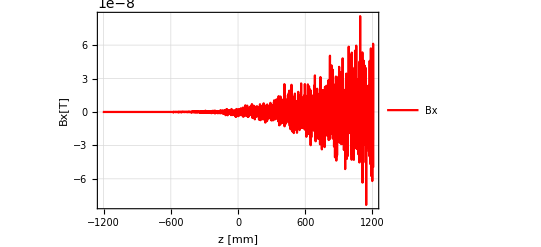
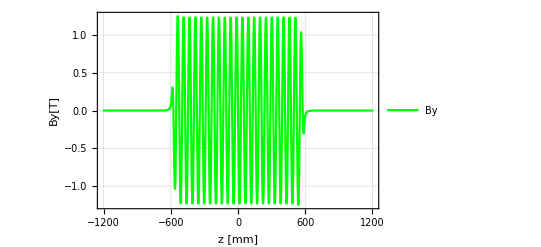
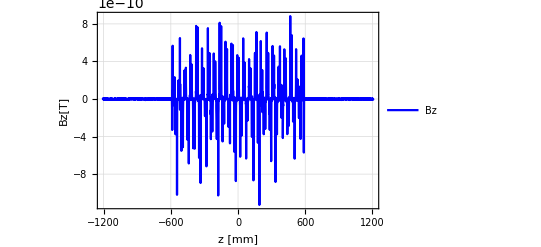

Horizontal field amplitude:    3.85412×10^-9 [T]

Vertical field amplitude:      1.20343 [T]

Longitudinal field amplitude:  6.47292×10^-10 [T]

Horizontal K: 5.90103

Vertical K:   1.88987×10^-8

IDInfo: elapsed time = 0.7656823 s

Fieldmap saved in file: Delta52.5_Fieldmap_H.txt

IDFieldMap: elapsed time = 2066.441873 s

```mathematica
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> 0];
IDShow[Device];
IDInfo[Device, λu];
Print[IDPlotFields[Device, "z", {Li, Lf}]];

mat = RadMatNdFeB[Br];
radMatApl[Device,mat];
RadSolve[Device,prec, maxiter];
IDInfo[Device, λu];
IDFieldMap["Delta52.5_Fieldmap_H.txt", Device, {Hi, Hf}, {0,0}, {Li, Lf}, Hnpts, 1, Lnpts ]
```

## Model (C)

IDDelta: elapsed time = 0.9063239 s

-Graphics3D-

IDShow: elapsed time = 1.531344 s

Horizontal field amplitude:    0.881381 [T]

Vertical field amplitude:      0.881119 [T]

Longitudinal field amplitude:  5.04418×10^-10 [T]

Horizontal K: 4.32057

Vertical K:   4.32185

IDInfo: elapsed time = 0.6406735 s

IDPlotFields: elapsed time = 18.081067 s

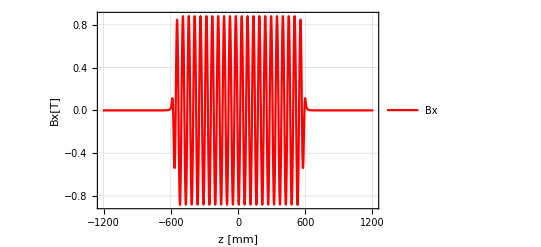
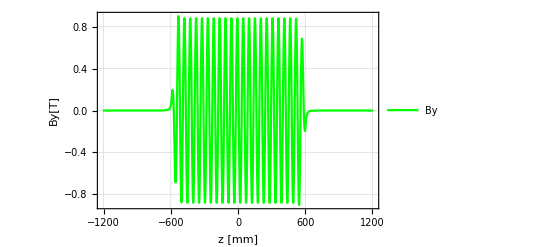
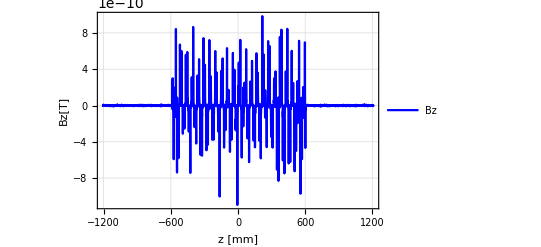

Horizontal field amplitude:    0.857619 [T]

Vertical field amplitude:      0.857367 [T]

Longitudinal field amplitude:  5.66646×10^-10 [T]

Horizontal K: 4.2041

Vertical K:   4.20533

IDInfo: elapsed time = 0.6719282 s

Fieldmap saved in file: Delta52.5_Fieldmap_C.txt

IDFieldMap: elapsed time = 1933.537042 s

```mathematica
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> λu/4];
IDShow[Device];
IDInfo[Device, λu];
Print[IDPlotFields[Device, "z", {Li, Lf}]];

mat = RadMatNdFeB[Br];
radMatApl[Device,mat];
RadSolve[Device,prec, maxiter];
IDInfo[Device, λu];
IDFieldMap["Delta52.5_Fieldmap_C.txt", Device, {Hi, Hf}, {0,0}, {Li, Lf}, Hnpts, 1, Lnpts ]
```